```mathematica
Build[SetP[7],setp7]
```

Building poset setp7  ...

Done

```mathematica
setp7
```

```mathematica
MobiusMatrixFromSets[Table[{k},{k,5}]]
```

Sort::normal: Nonatomic expression expected at position 1 in Sort[1].

General::stop: Further output of Sort::normal will be suppressed during this calculation.

{{1,If[{Sort[1]}=={Sort[2]},1,0],If[{Sort[1]}=={Sort[3]},1,0],If[{Sort[1]}=={Sort[4]},1,0],If[{Sort[1]}=={Sort[5]},1,0]},{If[{Sort[2]}=={Sort[1]},1,0],1,If[{Sort[2]}=={Sort[3]},1,0],If[{Sort[2]}=={Sort[4]},1,0],If[{Sort[2]}=={Sort[5]},1,0]},{If[{Sort[3]}=={Sort[1]},1,0],If[{Sort[3]}=={Sort[2]},1,0],1,If[{Sort[3]}=={Sort[4]},1,0],If[{Sort[3]}=={Sort[5]},1,0]},{If[{Sort[4]}=={Sort[1]},1,0],If[{Sort[4]}=={Sort[2]},1,0],If[{Sort[4]}=={Sort[3]},1,0],1,If[{Sort[4]}=={Sort[5]},1,0]},{If[{Sort[5]}=={Sort[1]},1,0],If[{Sort[5]}=={Sort[2]},1,0],If[{Sort[5]}=={Sort[3]},1,0],If[{Sort[5]}=={Sort[4]},1,0],1}}

```mathematica
SetsToSymbol[Table[{k},{k,5}],"n"]
```

n1x2x3x4x5

```mathematica
Table[
NeighborhoodGraph[ MobiusGraph5[k[[3]],k[[2]]],SetsToSymbol[Table[{v},{v,k[[1]]}],"n"],k[[1]]-1],
,{k,{{3,allGraphs3,K3Key},{4,allGraphs4,K4Key}}}]
```

Table::nliter: Non-list iterator Null at position 2 does not evaluate to a real numeric value.

```mathematica
ColorN[i_]:=Style[i,{Yellow,Blue,Red,Darker[Green]}[[i+1]]]
```

```mathematica
BetterGraph[g_]:=Graph[g,VertexLabels->Table[v->ColorN[VertexInDegree[g,v]],{v,VertexList[g]}]]
```

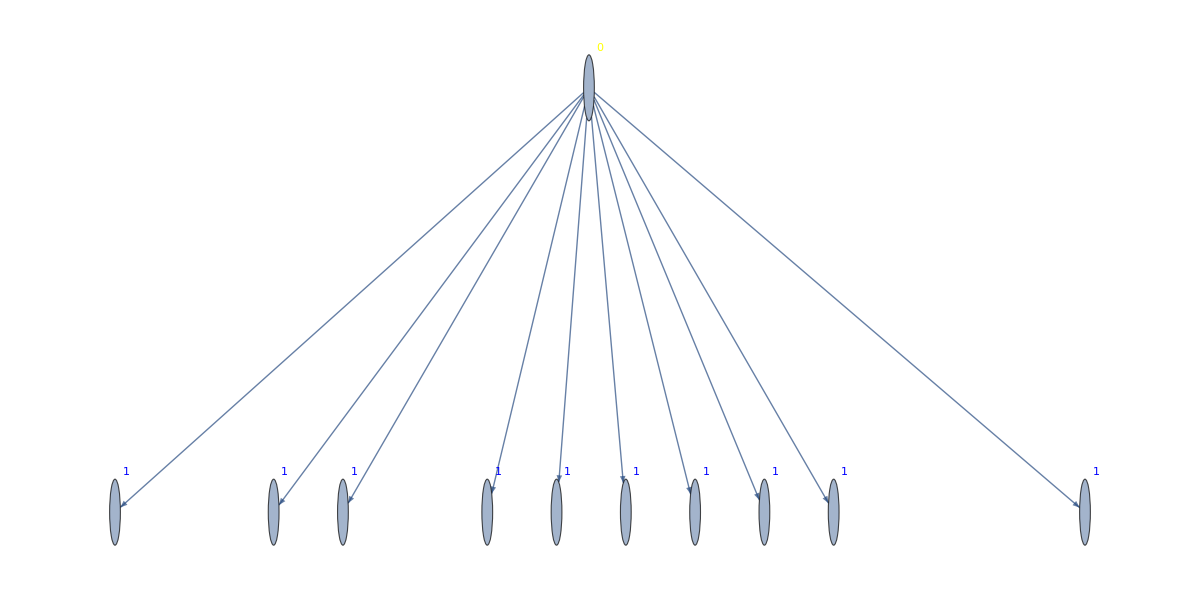
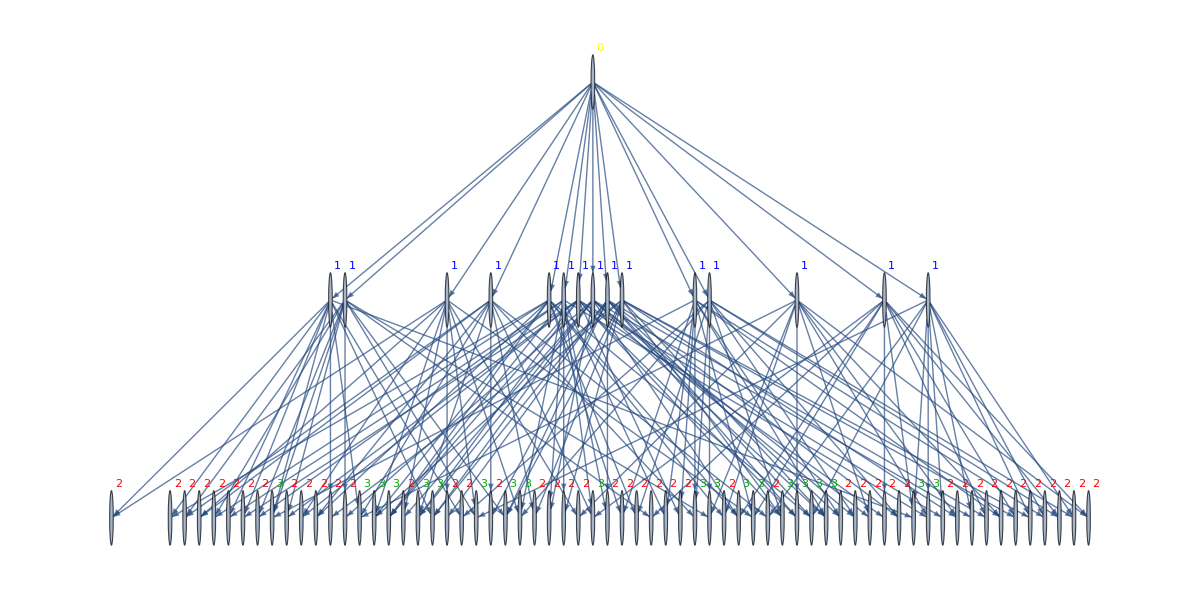

```mathematica
Table[BetterGraph[Graph[NeighborhoodGraph[MobiusGraph5[k⟦3⟧,k⟦2⟧],SetsToSymbol[Table[{v},{v,k⟦1⟧}],"n"],k⟦1⟧-4],GraphLayout->"LayeredDigraphEmbedding",ImageSize->1200,AspectRatio->1/2]],{k,{{5,allGraphs5,K5Key},{6,allGraphs6,K6Key}}}]
```

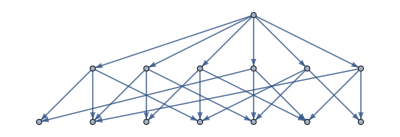

```mathematica
NeighborhoodGraph[ MobiusGraph5[K4Key,allGraphs4],n1x2x3x4,2]
```